## Functions

### General Functions

#### Sorting Data by Chromosome

```mathematica
nucleoMarkerSub[ftrs_]:=Transpose[
{
Transpose[ftrs][[1]],
Transpose[ftrs][[2]],
Transpose[ftrs][[3]],
Transpose[ftrs][[8]]
}
]
```

```mathematica
HistAlignRep[nucleosomeMarker_,chrs_]:=
Table[

SortBy[Select[nucleosomeMarker[[j]],#[[1]]==chrs[[i]]&],2]

,{i,1,Length[chrs]},{j,1,Length[nucleosomeMarker]}];
```

```mathematica
HistAlignRepSub[nucleosomeMarker_,chrs_]:=
Table[

nucleoMarkerSub[
SortBy[Select[nucleosomeMarker[[j]],#[[1]]==chrs[[i]]&],2]]

,{i,1,(Length[chrs]-1)},{j,1,Length[nucleosomeMarker]}];
```

#### Merge Functions

```mathematica
mergeChrPosExp[geneinf_,poslist_]:={geneinf[[1]],geneinf[[2]],geneinf[[3]],geneinf[[6]],geneinf[[7]],Select[poslist,#[[3]]==geneinf[[1]]&][[1,4]],Select[poslist,#[[3]]==geneinf[[1]]&][[1,5;;6]]}
```

### Sparse Matrix Functions

Generate sparse matrix with the features on some segment or whole chromosome. Length of segment is chrL, chrDomain is a list of start and end locations for a feature, and bpscale is the resolution. Note that the start and end

#### General Application

```mathematica
chrFeatureMap[chrL_,chrDomain_,bpscale_]:=
Total[
Table[
SparseArray[
i_/;
(Ceiling[chrDomain[[j,1]]])<i<(Ceiling[chrDomain[[j,2]]])->1,
Ceiling[chrL/bpscale],0
],{j,1,Length[chrDomain]}]
]
```

Below takes in the length of the chromosome, chrL_, a list of the domain coordinates in a paired list format of {start, stop}, a list of values, and the resolution to coarse grain to (bp_Scale)

```mathematica
chrFeatureMapValueScaled[chrL_,chrDomain_,val_,bpscale_ ]:=
Total[
Table[
SparseArray[
i_/;
Floor[chrDomain[[j,1]]/bpscale]<i<Ceiling[chrDomain[[j,2]]/bpscale]->val[[j]],
Ceiling[chrL/bpscale],0
],{j,1,Length[chrDomain]}]
]
```

mapToZeroMatrix [zeroMatrix_, dataMatrix_, normval_] :=

#### LAD Alignment

chrList is the index names for the chromosome element, chrLengths is a list of the lengths of each chromosome, lad1 is positions as a list of lists, lad2 is positions as a list of lists, bpscale is a scalar, defaulting to 1000 for resolution in Kb.

```mathematica
featureAlign[chrList_,chrLengths_, lad1_,lad2_,bpscale_]:=
Table[
{chrList[[ii]],
chrFeatureMap[
chrLengths[[ii]],
{#[[2]]/bpscale,#[[3]]/bpscale}&/@Select[lad1,StringMatchQ[#[[1]],chrList[[ii]]]&]
,bpscale
],
chrFeatureMap[
chrLengths[[ii]],
{#[[2]]/bpscale,#[[3]]/bpscale}&/@Select[lad2,StringMatchQ[#[[1]],chrList[[ii]]]&]
,bpscale
]
},
{ii,1,Length[chrList]}];
```

#### List of Feature Condition Alignment

```mathematica
featureAlignMultiple[chrList_,chrLengths_, chrft_,bpscale_]:=
Table[
{chrList[[ii]],
Table[
chrFeatureMap[
chrLengths[[ii]],
{#[[2]]/bpscale,#[[3]]/bpscale}&/@Select[chrft[[jj]],StringMatchQ[#[[1]],chrList[[ii]]]&]
,bpscale],{jj,1,Length[chrft]}]
},
{ii,1,Length[chrList]}];
```

#### Generate Empty Matrix

```mathematica
zeroMatrix[chromosome_,res_]:=Table[{res*i,res*j},{i,0,Ceiling[chromosome/res]},{j,0,Ceiling[chromosome/res]}]
```

### HiC Analysis Functions

#### Contact Scaling

```mathematica
distContact[hicData_]:=Transpose[{Transpose[hicData][[2]]-Transpose[hicData][[1]],Transpose[hicData][[3]]}];
```

```mathematica
scalingEst[tbl_,fn_]:={Transpose[tbl][[1,1]],fn[Transpose[tbl][[2]]]}
```

```mathematica
resScalingContacts[cond_,segs_]:=Table[MapIndexed[{#[[1]],#[[2]]/(segs)}&,cond[[i]]],{i,Length[cond]}]
```

resScalingContacts[cond_, segs_] := Table[MapIndexed[{#[[1]], #[[2]]/(segs*cond[[i, 1, 2]])} &, cond[[i]]], {i, Length[cond]}]

rescaling of the contacts is dividing the observed frequency / (number of segments in a chromosome * the contact count in the zero position)

```mathematica
resScalingContactsTotes[cond_]:=Table[MapIndexed[{#[[1]],#[[2]]/(Total[Transpose[cond[[i]]][[2]]])}&,cond[[i]]],{i,Length[cond]}]
```

```mathematica
resScalingContactsTotesSegments[cond_,totes_]:=Table[MapIndexed[{#[[1]],#[[2]]/totes[[i]]}&,cond[[i]]],{i,Length[cond]}]
```

### HiC to LAD Functions

#### Overlap Position

```mathematica
overlapHicLadIndex[hicIndex_,laminIndex_,lamidx_]:=
Flatten[Position[Table[hicIndex[[i,1,1]],{i,Length[hicIndex]}],_?(laminIndex[[lamidx,2]]<=#<=laminIndex[[lamidx,3]]&)],1]
```

```mathematica
overlapHicLadSelectByIndex[hicContacts_,hicidx_,lad_]:=Table[
Select[hicContacts[[hicidx[[i]]]],
((lad[[2]]<=#[[2]]<=lad[[3]]))&],
{i,Length[hicidx]}]
```

This is passing the contact matrix for a single chromosome for a single condition that has been arranged so that each segment is a subtable by the first position, hicidx is the position of a feature (in this class a position that contains values that fall within a LAD), and lad_ is the test coordinates (these can be anything of interest.

#### Overlap Values for start/end position

```mathematica
overlapHicLadSelect[hicValues_,laminIndex1_, laminIndex2_]:=
Select[Flatten[hicValues,1],(laminIndex1[[2]]<=#[[1]]<=laminIndex1[[3]])&&(laminIndex2[[2]]<=#[[2]]<=laminIndex2[[3]])&]
```

#### Scaling Measurement

```mathematica
lmFitHic[cond_,minidx_,maxidx_]:= Table[
LinearModelFit[Log@cond[[i,Position[cond[[i]],_?(#==minidx&)][[1,1]];;Position[cond[[i]],_?(#==maxidx&)][[1,1]]]], x,x]
,{i,Length[cond]}]
```

```mathematica
f0FitHic[lmvals_]:=Table[Normal[lmvals[[i]]]/.x->Log[x]//Exp,{i,Length[lmvals]}]
```

## Generated Data

### Already Generated

```mathematica
dir = SetDirectory@NotebookDirectory[]
```

/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/hic data/Repeat Download/Merge Results

#### HiC If Generated

```mathematica
tDone = FileNames["*.m",StringJoin[dir,"/Analysis/"],3];
```

```mathematica
tDone[[1]]
```

/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/hic data/Repeat Download/Merge Results/Analysis/All/chr10.m

#### Load Data

```mathematica
chrToCheck =1;
tDoneChr = Select[tDone, StringContainsQ[StringJoin["/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]], ".m"]]]
```

{/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/hic data/Repeat Download/Merge Results/Analysis/All/chr1.m,/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/hic data/Repeat Download/Merge Results/Analysis/Lbb1/acrossLad/chr1.m,/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/hic data/Repeat Download/Merge Results/Analysis/Lbb1/acrossNotLad/chr1.m,/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/hic data/Repeat Download/Merge Results/Analysis/Lbb1/withinLad/chr1.m,/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/hic data/Repeat Download/Merge Results/Analysis/Lbb1/withinNotLad/chr1.m}

```mathematica
allContactsVar = Import[Select[tDoneChr,StringContainsQ["All"]][[1]]];
```

```mathematica
contDistCondMean = Table[scalingEst[allContactsVar[[i,j]],Total[#]&],{i,Length[allContactsVar]},{j,Length[allContactsVar[[i]]]}];
```

## Analysis of Contacts within specific markers

### Load LAD and HiC Data

```mathematica
dir = SetDirectory@NotebookDirectory[]
```

#### General Organization

```mathematica
chrsLengths = Table[GenomeData[i,"SequenceLength"],{i,1,24}];
chrList =Flatten[Append[Table[StringJoin["chr",ToString[i]],{i,1,22}],{"chrX","chrY"}]];
chrList2 =Flatten[Append[Table[StringJoin["Chromosome",ToString[i]],{i,1,22}],{"ChromosomeX","ChromosomeY"}]];
chrList3  =Flatten[Append[Table[i,{i,1,22}],{"X","Y"}]];
m=1000;
```

```mathematica
chrsLengthsHg38 = {248956422,242193529,198295559,190214555,181538259,170805979,159345973,145138636,138394717,133797422,135086622,133275309,114364328,107043718,101991189,90338345,83257441,80373285,58617616,64444167,46709983,50818468,156040895,57227415};
```

chrsLengthsHg38 was input from https://www.ncbi.nlm.nih.gov/grc/human/data

```mathematica
chrsLengthsHg38[[chrToCheck]]
chrsLengthsHg38[[16;;18]]
```

181538259

{90338345,83257441,80373285}

## Intrachromosomal Analysis Portions

### Hi-C vs Lad Contact Scaling

#### HiC Data within a Chromosome

```mathematica
t1 = FileNames["*.csv",StringJoin[dir,"/"],2];
```

```mathematica
chrToCheck = 1;
t2 = Select[t1, StringContainsQ[StringJoin["/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]], ".csv"]]]
```

{/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/hic data/Repeat Download/Merge Results/Auxin/chr1.csv,/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/hic data/Repeat Download/Merge Results/Untreated/chr1.csv}

```mathematica
hicForChromosome = Import[#,"Data", "Numeric"->True, Delimiter->","]&/@t2;
Length[#]&/@hicForChromosome
```

{8800860,9931460}

```mathematica
contactsByFirstPos = Table[SplitBy[hicForChromosome[[i]],#[[1]]&],{i,Length[hicForChromosome]}];
```

#### Fidelity Checks

```mathematica
Intersection[hicForChromosome[[1]],hicForChromosome[[2]]]
```

{{76225000,115350000,0.66008},{165500000,170350000,0.765984}}

```mathematica
Dimensions[hicForChromosome[[2]]]
```

{9931460,3}

#### All Contacts

```mathematica
contDistCond = SplitBy[Sort[#],First]&/@Table[distContact[hicForChromosome[[i]]],{i,1,Length[hicForChromosome]}];
```

```mathematica
contDistCondMean = Table[scalingEst[contDistCond[[i,j]],Total[#]&],{i,Length[contDistCond]},{j,Length[contDistCond[[i]]]}];
```

```mathematica
chrToCheck
```

1

#### Export

```mathematica
Export[StringJoin[dir,"/Analysis/All/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]],".m"],contDistCond]
```

### Normalize and Fit Contacts Data

```mathematica
fitRange = {100000,1000000};
segVals = Table[Total[Transpose[contDistCondMean[[i]]][[2]]],{i,Length[contDistCondMean]}];
```

#### All Contacts

```mathematica
contDistCondMeanScaled = resScalingContactsTotesSegments[contDistCondMean, segVals];
```

```mathematica
allContactLmFit = lmFitHic[contDistCondMeanScaled,fitRange[[1]],fitRange[[2]]];
allContactF0Fit=f0FitHic[allContactLmFit];
```

```mathematica
dApproxAllCont = Table[3/allContactLmFit[[i,1,2,2]],{i,Length[allContactLmFit]}]
sValAllCont = Table[Abs[allContactLmFit[[i,1,2,2]]],{i,Length[allContactLmFit]}]
```

{-3.09961,-2.92381}

{0.967863,1.02606}

## Visualize Results

### Scaling

#### Coloring Variables

```mathematica
outsideTheme={Directive[Purple, PointSize[.015]],Directive[Blue, PointSize[.015]],Directive[Black, PointSize[.015]]}
insideTheme={Directive[Red, PointSize[.015]],Directive[Orange, PointSize[.015]],Directive[Green, PointSize[.015]]}
```

{Directive[RGBColor[0.5, 0, 0.5],PointSize[0.015]],Directive[RGBColor[0, 0, 1],PointSize[0.015]],Directive[GrayLevel[0],PointSize[0.015]]}

{Directive[RGBColor[1, 0, 0],PointSize[0.015]],Directive[RGBColor[1, 0.5, 0],PointSize[0.015]],Directive[RGBColor[0, 1, 0],PointSize[0.015]]}

```mathematica
allTheme = {Directive[Brown, PointSize[.015]],Directive[Cyan, PointSize[.015]],Directive[Magenta, PointSize[.025]]}
```

{Directive[RGBColor[0.6, 0.4, 0.2],PointSize[0.015]],Directive[RGBColor[0, 1, 1],PointSize[0.015]],Directive[RGBColor[1, 0, 1],PointSize[0.025]]}

```mathematica
fitTheme =  {Directive[Black, Thickness[.0075]],Directive[Gray, Thickness[.0075]]}
```

{Directive[GrayLevel[0],Thickness[0.0075]],Directive[GrayLevel[0.5],Thickness[0.0075]]}

#### Scaled with Fit

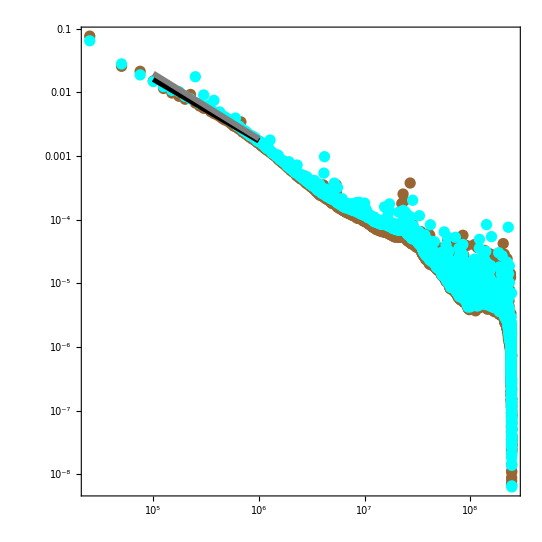

```mathematica
Show[{
ListLogLogPlot[contDistCondMeanScaled, PlotStyle->allTheme, AxesStyle->Directive[Black,Bold, 24], AxesOrigin->{7500,0}, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,24], AspectRatio->1],
LogLogPlot[allContactF0Fit[[1]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[1]]],
LogLogPlot[allContactF0Fit[[2]],{x,fitRange[[1]],fitRange[[2]]},  PlotStyle->fitTheme[[2]]]}, PlotRange->All]
```